The governing ODE we get for steady-state motion of the frictional landslide governed by a linear friction law:  is

where  is the average slope of the landslide body. 
If we define the landslide thickness , our ODE is now:

```mathematica
eqnODE = H[x]*H'[x] - (Tan[θ]*(1+b''[x]/2*H[x])/(1+b'[x]*Tan[θ])-b'[x]-f)*H[x]== -η (x^2/2+x)
```

H[x] H'[x]-H[x] (-f-b'[x]+(Tan[θ] (1+1/2 H[x] b''[x]))/(1+Tan[θ] b'[x]))==-((x+x^2/2) η)

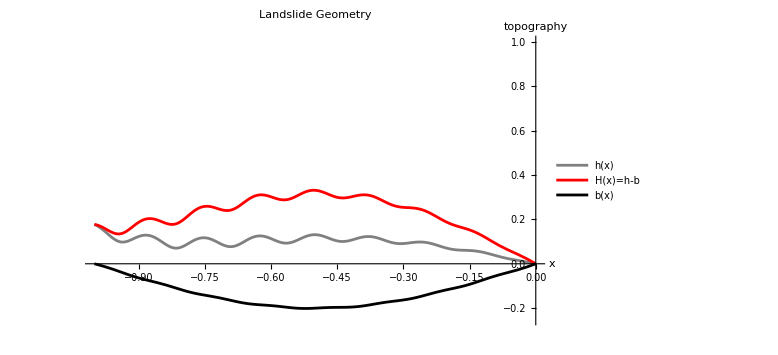

```mathematica
bv = 0.2*(Sin[ π x] + 0.01*Sin[16π x]);(*add 5% perturbation to topography at shorter wavelengths*)
θv = π/4;
fv= 0.1;
ηv = -1;(*Effective erosion rate: this should be negative*)
eqn = H[x]*H'[x] - (Tan[θv]*(1+D[bv,x,x]/2*H[x])/(1+D[bv,x]*Tan[θv])-D[bv,x]-fv)*H[x]== -ηv (x^2/2+x);
(*We will assume that erosion varies linearly over the domain from 0 (at x=-1)-> max (at x = 0)*)
solss = NDSolve[{eqn,H[0]==10^-9},H,{x,-1,0}];
h = bv+ H[x]/. solss;
p1=Plot[{h,H[x]/. solss,bv},{x,-1,0},PlotStyle->{{Gray,Thick},{Red},{Black,Thick}},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","b(x)"},ImageSize->Large,PlotRange->{-0.25,1}]
```

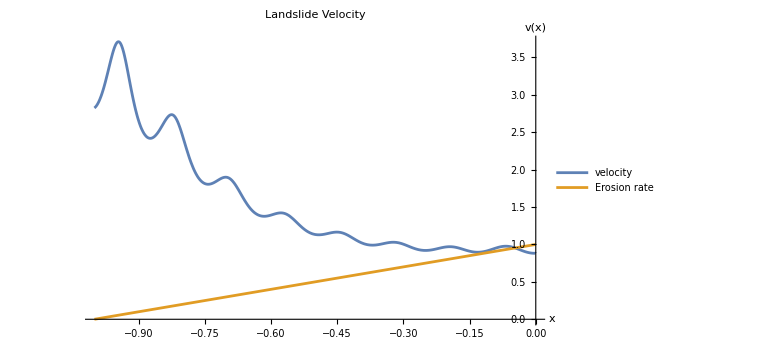

```mathematica
vx = (Tan[θv]*(1+D[bv,x,x]/2*H[x]/.solss)/(1+D[bv,x]*Tan[θv])-D[h,x]-fv);
p2=Plot[{vx,-ηv(1+x)},{x,-1,0},PlotRange->Full,PlotLabel->"Landslide Velocity",AxesLabel->{"x","v(x)"},PlotLegends->{"velocity","Erosion rate"},ImageSize->Large]
```

```mathematica
Export["~/Documents/GitHub/landslides/analyticsol/landslide_topography.png",p1]
Export["~/Documents/GitHub/landslides/analyticsol/landslide_vel.png",p2]
```

~/Documents/GitHub/landslides/analyticsol/landslide_topography.png

~/Documents/GitHub/landslides/analyticsol/landslide_vel.png